```mathematica
Clear["Global`*"]
kHz=10^3;
nm=10^-9;
mK=10^-3;
uK=10^-6;
us=10^-6;
kB=1.38064852 10^-23;
ℏ=1.0545718 10^-34;
amu=1.66054 10^-27;
λtrap=970 nm;
m=132.90545 amu;
T=8uK;
nbar=1/(Exp[(ℏ 2π f)/(kB T)]-1)/.f->{20,105,123}kHz
```

{7.84464,1.1397,0.916166}

{0.886937^n,0.532645^n,0.478125^n}

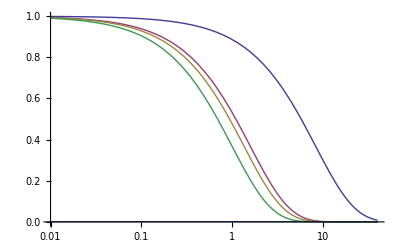

```mathematica
pn = nbar^n/(1+nbar)^n
LogLinearPlot[{pn,Exp[-n],.001},{n,0.01,40},PlotRange->All]
```

```mathematica
P0=1/(1+nbar);
pn = nbar^n/(1+nbar)^n(*ratio of Pn to P0*)
```

{0.886937^n,0.532645^n,0.478125^n}

```mathematica
nbar; 
n=(2{1/2,1,2,3,4})^2;
Pn;
ωn=√n;(*ratio of cooling sideband rabi freq to gnd state sideband rabi freq*)
tπ=1/√n;
```

```mathematica
Join[{n},{tπ},pn]//TableForm
```

1 | 4 | 16 | 36 | 64
1 | 1/2 | 1/4 | 1/6 | 1/8
0.886937 | 0.61883 | 0.146651 | 0.0133089 | 0.000462534
0.532645 | 0.0804915 | 0.0000419759 | 1.41824×10^-10 | 3.10457×10^-18
0.478125 | 0.0522594 | 7.45861×10^-6 | 2.90723×10^-12 | 3.09479×10^-21

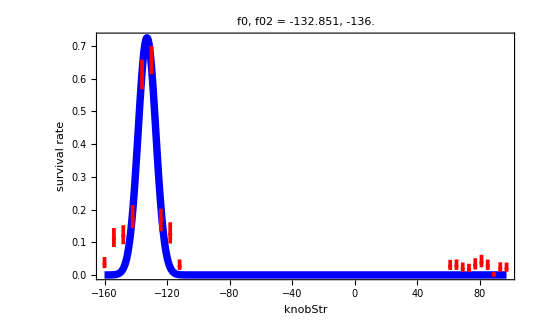

0.0956905

```mathematica
Clear["Global`*"]
Needs["ErrorBarLogPlots`"]

dat={{{-160.,0.03389830508474576},ErrorBar[{-0.01312855764059765,0.02096219957194647}]},{{-154.,0.1111111111111111},ErrorBar[{-0.02582230903213978,0.03241364613195147}]},{{-148.,0.12},ErrorBar[{-0.02609066796967023,0.0321224140014163}]},{{-142.,0.17543859649122806},ErrorBar[{-0.032756897219926084,0.0384014433679048}]},{{-136.,0.6140350877192983},ErrorBar[{-0.04639885625033524,0.044415637333477975}]},{{-130.,0.6583333333333333},ErrorBar[{-0.04444370527425345,0.04182662538444626}]},{{-124.,0.16521739130434782},ErrorBar[{-0.03171596691247436,0.03748808085550287}]},{{-118.,0.125},ErrorBar[{-0.02890043261187107,0.03604328975472826}]},{{-112.,0.02727272727272727},ErrorBar[{-0.011776679632342591,0.020294288149951104}]},{{61.,0.02654867256637168},ErrorBar[{-0.011465767187734519,0.019771930826920976}]},{{65.,0.02727272727272727},ErrorBar[{-0.011776679632342591,0.020294288149951104}]},{{69.,0.019230769230769232},ErrorBar[{-0.009584333281451434,0.0187418424389606}]},{{73.,0.017241379310344827},ErrorBar[{-0.008595749969405632,0.01684803408375872}]},{{77.,0.029411764705882353},ErrorBar[{-0.012694630497078054,0.021832266133857046}]},{{81.,0.0380952380952381},ErrorBar[{-0.01473917822228369,0.023454362409165985}]},{{85.,0.02702702702702703},ErrorBar[{-0.011671185578575964,0.0201171315245219}]},{{89.,0.},ErrorBar[{0.,0.008695652173913044}]},{{93.,0.0196078431372549},ErrorBar[{-0.00977163580311849,0.019099638848997035}]},{{97.,0.019230769230769232},ErrorBar[{-0.009584333281451434,0.0187418424389606}]}};

RSB=Cases[dat,x_/;x[[1,1]]<0];
gauss2=A Exp[-(f-f0)^2/(2 σ0^2)]+0 Exp[-(f-f02)^2/(2 σ02^2)];
{offs0,A0,f00,σ00,A200,f020,σ020}={0,.2,-158,8,.7,-136,8};

nlm=NonlinearModelFit[RSB[[;;,1]],gauss2,{{ offs,offs0},{ A,A0}, {f0,f00}, {σ0,σ00},{ A2,A200}, {f02,f020}, {σ02,σ020}},f(*,Weights->weights*)];
fit=nlm["BestFitParameters"];

Show[{
Plot[
gauss2/.fit,{f,dat[[1,1,1]],dat[[-1,1,1]]},PlotStyle->{Thickness[.01],Blue},Frame->{True,True},Axes->False,FrameLabel->{knobStr,"survival rate"},PlotRange->All,PlotLabel->"f0, f02 = " <>ToString[f0/.fit]<>", "<>ToString[f02/.fit] 
],

ErrorListPlot[dat,PlotStyle->{Thickness[.005],Red},Frame->{True,True},Axes->False]
}]
(*calculate nbar*)
ARSB=Re[Integrate[gauss2(*A2 Exp[-(f-f02)^2/(2 σ02^2)]*)/.fit,{f,-Infinity,Infinity}]];
BSB=Cases[dat,x_/;x[[1,1]]>0];
Δf=Mean[Differences[BSB[[;;,1]][[;;,1]]]];
ABSB=Total[BSB[[;;,1]][[;;,2]]]Δf;
nbar=1/(ARSB/ABSB-1)
```

```mathematica
Δnbar=√((D[nbar, σ0])^2(#[[4]])^2+(D[nbar, A])^2(#[[2]])^2+(D[nbar, σ02])^2(#[[7]])^2+(D[nbar, A2])^2(#[[5]])^2)&@nlm["ParameterErrors"]/.fit;
```

```mathematica
errs=Differences[#]&/@Cases[
ToExpression[StringSplit[ToString[dat[[;;,2]]],{"ErrorBar[","]"}]]
,x_/;x∈Reals]
```

```mathematica
RandomSample[Range[-60,25,5]]
```

{-45,-60,0,10,-15,-50,-10,-20,-55,20,-25,-35,-5,-30,25,-40,5,15}

```mathematica
8.57(.35*4+.35*3)
```

20.9965

```mathematica
8.57(.35*3+.35*2)
```

14.9975